```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0},
M=2;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
Print["q/(2πϵ0)=",q/(2π ϵ0)];
Print[NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]]];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273492-0.00214368 ⅈ and 0.0243771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0027378-0.00294045 ⅈ and 0.034719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.03855×10^-7-0.000538534 ⅈ and 0.0047202 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

q/(2πϵ0)=2.61283×10^16

{{ϕ[0]→434.512-160.588 ⅈ,ϕ[1]→-2.61283×10^16-0.481066 ⅈ,A[-2]→-55657.-28386.9 ⅈ,A[-1]→17894.8+31254.1 ⅈ,A[1]→298.418+1976.29 ⅈ,A[2]→-407.592-659.672 ⅈ,B[-2]→40.91+36.0107 ⅈ,B[-1]→-762.426-904.681 ⅈ,B[1]→-7253.67-62400.7 ⅈ,B[2]→365078.+613803. ⅈ}}

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0},
M=3;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
Print["q/(2πϵ0)=",q/(2π ϵ0)];
Print[NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]]];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.26921×10^-7-0.00046044 ⅈ and 0.00665807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.796988}. NIntegrate obtained 4.46291×10^-7-0.000736704 ⅈ and 0.0118443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273492-0.00214368 ⅈ and 0.0243771 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

q/(2πϵ0)=2.61283×10^16

{{ϕ[0]→-1363.54-1290.63 ⅈ,ϕ[1]→-2.61283×10^16+0.813362 ⅈ,A[-3]→471391.-211347. ⅈ,A[-2]→-155384.+50736.6 ⅈ,A[-1]→13990.2+12018.2 ⅈ,A[1]→-1319.12+1901.67 ⅈ,A[2]→45.3971-145.962 ⅈ,A[3]→8.72559-16.1345 ⅈ,B[-3]→-36.2225-3.12599 ⅈ,B[-2]→240.909-59.1384 ⅈ,B[-1]→-315.005-237.091 ⅈ,B[1]→35825.9-58583.8 ⅈ,B[2]→14468.4+136181. ⅈ,B[3]→-410069.+470205. ⅈ}}

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0},
M=4;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
Print["q/(2πϵ0)=",q/(2π ϵ0)];
Print[NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]]];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.21834×10^-6-0.000459109 ⅈ and 0.0478578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.98249×10^-6-0.00243917 ⅈ and 0.0668455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.26921×10^-7-0.00046044 ⅈ and 0.00665807 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

q/(2πϵ0)=2.61283×10^16

{{ϕ[0]→-1671.33-2157.81 ⅈ,ϕ[1]→-2.61283×10^16-1.61633 ⅈ,A[-4]→320608.-854653. ⅈ,A[-3]→566049.+625704. ⅈ,A[-2]→-13725.3-33537.5 ⅈ,A[-1]→-14582.7-11211.7 ⅈ,A[1]→-1227.55-127.527 ⅈ,A[2]→-73.7931-306.333 ⅈ,A[3]→30.3542+39.6376 ⅈ,A[4]→-3.81922-2.66893 ⅈ,B[-4]→0.429674+0.294079 ⅈ,B[-3]→-24.1309-46.3129 ⅈ,B[-2]→67.4694+128.682 ⅈ,B[-1]→906.644+1089.6 ⅈ,B[1]→26016.4-10290.2 ⅈ,B[2]→114982.+331195. ⅈ,B[3]→-901498.-968391. ⅈ,B[4]→2.96796×10^6+1.2314×10^6 ⅈ}}

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0},
M=5;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
Print["q/(2πϵ0)=",q/(2π ϵ0)];
Print[NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]]];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 4.40538×10^-7-0.000356909 ⅈ and 0.0215196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.21834×10^-6-0.000459109 ⅈ and 0.0478578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.98249×10^-6-0.00243917 ⅈ and 0.0668455 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

q/(2πϵ0)=2.61283×10^16

{{ϕ[0]→2153.77-2151.16 ⅈ,ϕ[1]→-2.61283×10^16-0.215441 ⅈ,A[-5]→-1.74048×10^6+9.90354×10^6 ⅈ,A[-4]→-773138.+829733. ⅈ,A[-3]→791504.+336537. ⅈ,A[-2]→-131233.+169552. ⅈ,A[-1]→54234.6-82368. ⅈ,A[1]→2745.+2042.61 ⅈ,A[2]→-447.342-842.117 ⅈ,A[3]→62.5881+128.061 ⅈ,A[4]→-5.84201-10.0606 ⅈ,A[5]→0.366548+0.351546 ⅈ,B[-5]→-0.0770265+0.493176 ⅈ,B[-4]→0.776237+1.304 ⅈ,B[-3]→-8.39938-43.2182 ⅈ,B[-2]→287.113+26.3691 ⅈ,B[-1]→-1432.25+3229.41 ⅈ,B[1]→-104348.-66587.6 ⅈ,B[2]→481528.+702727. ⅈ,B[3]→-1.65823×10^6-2.55195×10^6 ⅈ,B[4]→4.11192×10^6+4.3495×10^6 ⅈ,B[5]→-7.53859×10^6-2.58709×10^6 ⅈ}}

```mathematica
TransformedField["Polar"->"Cartesian",m(Bm/r^(m+1)-Am r^(m-1))Exp[I m θ],{r,θ}->{x,y}]
```

-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-Bm+Am (x^2+y^2)^m)

```mathematica
TransformedField["Polar"->"Cartesian",ϕ1/r,{r,θ}->{x,y}]
```

ϕ1/(√(x^2+y^2))

```mathematica
TransformedField["Polar"->"Cartesian",-I m (Am r^(m-1)+Bm/r^(m+1))Exp[I m θ],{r,θ}->{x,y}]
```

-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (Bm+Am (x^2+y^2)^m)

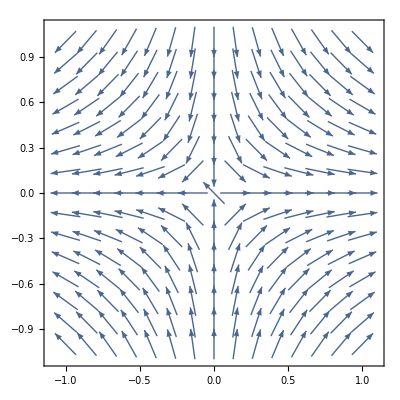

```mathematica
VectorPlot[{x/Sqrt[x^2+y^2],-y/Sqrt[x^2+y^2]},{x,-1,1},{y,-1,1}]
```

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=5;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
Print["q/(2πϵ0)=",q/(2π ϵ0)];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Table[{Re[(Er[x,y]x-Et[x,y]y)/Sqrt[x^2+y^2]],Re[(Er[x,y]y+Et[x,y]x)/Sqrt[x^2+y^2]]},
{x,0.01R,0.97R,0.2R},{y,0.01R,0.97R,0.2R}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 4.40538×10^-7-0.000356909 ⅈ and 0.0215196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.21834×10^-6-0.000459109 ⅈ and 0.0478578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.98249×10^-6-0.00243917 ⅈ and 0.0668455 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

q/(2πϵ0)=2.61283×10^16

{{ϕ[0]→2153.77-2151.16 ⅈ,ϕ[1]→-2.61283×10^16-0.215441 ⅈ,A[-5]→-1.74048×10^6+9.90354×10^6 ⅈ,A[-4]→-773138.+829733. ⅈ,A[-3]→791504.+336537. ⅈ,A[-2]→-131233.+169552. ⅈ,A[-1]→54234.6-82368. ⅈ,A[1]→2745.+2042.61 ⅈ,A[2]→-447.342-842.117 ⅈ,A[3]→62.5881+128.061 ⅈ,A[4]→-5.84201-10.0606 ⅈ,A[5]→0.366548+0.351546 ⅈ,B[-5]→-0.0770265+0.493176 ⅈ,B[-4]→0.776237+1.304 ⅈ,B[-3]→-8.39938-43.2182 ⅈ,B[-2]→287.113+26.3691 ⅈ,B[-1]→-1432.25+3229.41 ⅈ,B[1]→-104348.-66587.6 ⅈ,B[2]→481528.+702727. ⅈ,B[3]→-1.65823×10^6-2.55195×10^6 ⅈ,B[4]→4.11192×10^6+4.3495×10^6 ⅈ,B[5]→-7.53859×10^6-2.58709×10^6 ⅈ}}

{{{-4.99235×10^14,3.60535×10^14},{3.52533×10^7,4.01127×10^7},{330491.,581138.},{17259.2,-6434.37},{3960.49,-27181.6}},{{-1.27612×10^7,-4.73561×10^7},{-5.6103×10^6,3.31832×10^6},{-178359.,-410038.},{-6643.71,-67258.1},{-3579.15,-29263.1}},{{-216421.,-864353.},{356190.,366904.},{-119957.,85952.2},{-43858.1,-14067.3},{-12856.2,-16625.9}},{{-11103.1,-90153.5},{74527.9,7021.44},{199.679,41435.3},{-17562.4,10565.9},{-9316.06,-2742.49}},{{-922.331,-19543.7},{15714.5,-4075.14},{5485.01,11111.2},{-4116.38,8468.73},{-3768.12,3237.65}}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 4.40538×10^-7-0.000356909 ⅈ and 0.0215196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -7.21834×10^-6-0.000459109 ⅈ and 0.0478578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.98249×10^-6-0.00243917 ⅈ and 0.0668455 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

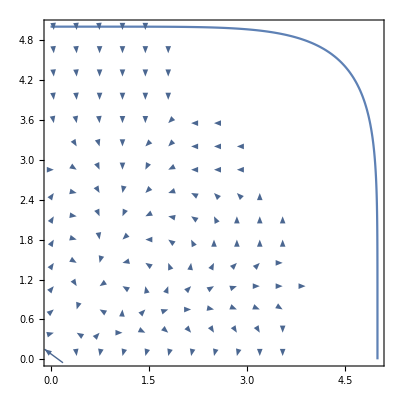

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=5;(* Half the number of coefficients Am or Bm *)
n=6;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Re[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Re[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}}]
]
```